```mathematica
f1[a_]=6/Pi/Pi*Sum[1/(m*m+a),{m, 1,∞}]
f2[a_]=6/(Pi*Pi*Sqrt[a])*(Pi/2-ArcTan[6/Pi/Pi/Sqrt[a]])
```

(3 (-1+√a π Coth[√a π]))/(a π^2)

(6 (π/2-ArcTan[6/(√a π^2)]))/(√a π^2)

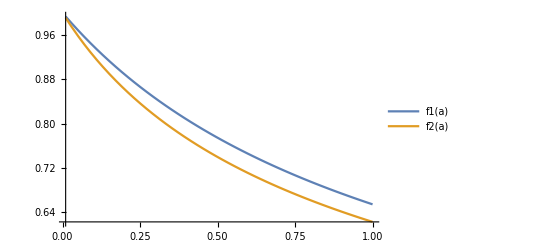

```mathematica
Plot[{f1[a],f2[a]},{a,0.01,1},PlotLegends->"Expressions"]
```

```mathematica
6/Pi/Pi*Sum[Exp[-a*n*n]/n*n,{n,1,∞}]
```

(3 (-1+EllipticTheta[3,0,ⅇ^-a]))/π^2

```mathematica
Plot[(3 (-1+EllipticTheta[3,0,ⅇ^-a]))/π^2,{a,-8,8}]
```